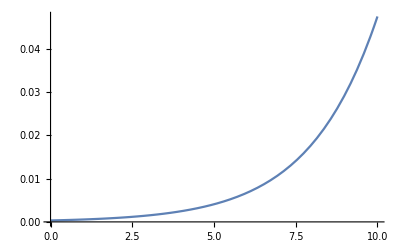

```mathematica
avgk = 8;
trophicload=2;
probext = 1/(1 + Exp[-0.5*(Np-(trophicload*avgk))]);
Plot[probext,{Np,0,10}]
```

10

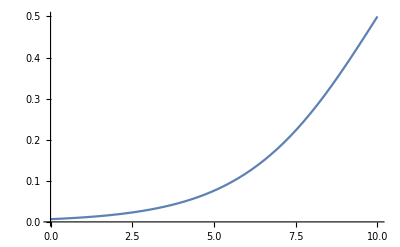

```mathematica
tl=10
probext2 = 1/(1 + Exp[-0.5*(Np-tl)]);
Plot[probext2,{Np,0,10}]
```

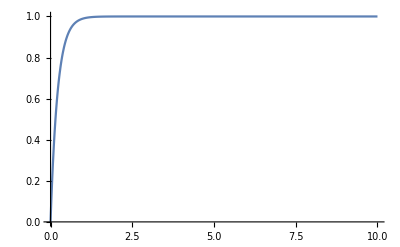

```mathematica
Plot[1-0.01^n-(1-0.01)^1000,{n,0,10},PlotRange->{0,1}]
```

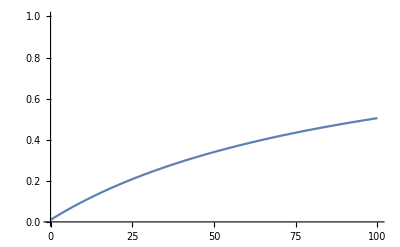

```mathematica
baseline=0.01;
Plot[baseline+ (1-baseline)*(1 - 1/(1+0.01n)),{n,0,100},PlotRange->{0,1}]
```

```mathematica
Solve[{
0 == e1*a1*(R+R1)*P1-m1*P1,
0 ==e2*a2*(R+R2)*P2-m2*P2,
0 == r*R*(1-R)-a1*R*P1-a2*R*P2,
0 == r1*R1*(1-R1)-a1*R1*P1,
0 == r2*R2*(1-R2)-a2*R2*P2
},{R,P1,P2,R1,R2}]
```

{{R→0,P1→0,P2→0,R1→1,R2→1},{R→1,P1→0,P2→0,R1→0,R2→0},{R→1,P1→0,P2→0,R1→1,R2→0},{R→1,P1→0,P2→0,R1→1,R2→1},{R→0,P1→0,P2→0,R1→1,R2→0},{R→-(-a2 e2 r+a2 e2 r2-m2 r2)/(a2 e2 (r+r2)),P1→0,P2→((2 a2 e2 r-m2 r) r2)/(a2^2 e2 (r+r2)),R1→0,R2→-(a2 e2 r-m2 r-a2 e2 r2)/(a2 e2 (r+r2))},{R→-(-a2 e2 r+a2 e2 r2-m2 r2)/(a2 e2 (r+r2)),P1→0,P2→((2 a2 e2 r-m2 r) r2)/(a2^2 e2 (r+r2)),R1→1,R2→-(a2 e2 r-m2 r-a2 e2 r2)/(a2 e2 (r+r2))},{R→m2/(a2 e2),P1→0,P2→((a2 e2-m2) r)/(a2^2 e2),R1→0,R2→0},{R→m2/(a2 e2),P1→0,P2→((a2 e2-m2) r)/(a2^2 e2),R1→1,R2→0},{R→1,P1→0,P2→0,R1→0,R2→1},{R→0,P1→0,P2→0,R1→0,R2→1},{R→-(-a1 e1 r+a1 e1 r1-m1 r1)/(a1 e1 (r+r1)),P1→((2 a1 e1 r-m1 r) r1)/(a1^2 e1 (r+r1)),P2→0,R1→-(a1 e1 r-m1 r-a1 e1 r1)/(a1 e1 (r+r1)),R2→0},{R→-(-a1 e1 r+a1 e1 r1-m1 r1)/(a1 e1 (r+r1)),P1→((2 a1 e1 r-m1 r) r1)/(a1^2 e1 (r+r1)),P2→0,R1→-(a1 e1 r-m1 r-a1 e1 r1)/(a1 e1 (r+r1)),R2→1},{R→m1/(a1 e1),P1→((a1 e1-m1) r)/(a1^2 e1),P2→0,R1→0,R2→0},{R→m1/(a1 e1),P1→((a1 e1-m1) r)/(a1^2 e1),P2→0,R1→0,R2→1},{R→0,P1→0,P2→((a2 e2-m2) r2)/(a2^2 e2),R1→1,R2→m2/(a2 e2)},{R→0,P1→((a1 e1-m1) r1)/(a1^2 e1),P2→0,R1→m1/(a1 e1),R2→1},{R→0,P1→((a1 e1-m1) r1)/(a1^2 e1),P2→0,R1→m1/(a1 e1),R2→0},{R→0,P1→((a1 e1-m1) r1)/(a1^2 e1),P2→((a2 e2-m2) r2)/(a2^2 e2),R1→m1/(a1 e1),R2→m2/(a2 e2)},{R→0,P1→0,P2→((a2 e2-m2) r2)/(a2^2 e2),R1→0,R2→m2/(a2 e2)},{R→-(-a1 a2 e1 e2 r+a1 a2 e1 e2 r1-a2 e2 m1 r1+a1 a2 e1 e2 r2-a1 e1 m2 r2)/(a1 a2 e1 e2 (r+r1+r2)),P1→(r1 (2 a1 a2 e1 e2 r-a2 e2 m1 r-a2 e2 m1 r2+a1 e1 m2 r2))/(a1^2 a2 e1 e2 (r+r1+r2)),P2→((2 a1 a2 e1 e2 r-a1 e1 m2 r+a2 e2 m1 r1-a1 e1 m2 r1) r2)/(a1 a2^2 e1 e2 (r+r1+r2)),R1→-(a1 a2 e1 e2 r-a2 e2 m1 r-a1 a2 e1 e2 r1-a1 a2 e1 e2 r2-a2 e2 m1 r2+a1 e1 m2 r2)/(a1 a2 e1 e2 (r+r1+r2)),R2→-(a1 a2 e1 e2 r-a1 e1 m2 r-a1 a2 e1 e2 r1+a2 e2 m1 r1-a1 e1 m2 r1-a1 a2 e1 e2 r2)/(a1 a2 e1 e2 (r+r1+r2))},{R→m1/(a1 e1),P1→-(-a1 a2 e1 e2 r+a2 e2 m1 r+a1 a2 e1 e2 r2+a2 e2 m1 r2-a1 e1 m2 r2)/(a1^2 a2 e1 e2),P2→((a1 a2 e1 e2+a2 e2 m1-a1 e1 m2) r2)/(a1 a2^2 e1 e2),R1→0,R2→-(a2 e2 m1-a1 e1 m2)/(a1 a2 e1 e2)},{R→m2/(a2 e2),P1→((a1 a2 e1 e2-a2 e2 m1+a1 e1 m2) r1)/(a1^2 a2 e1 e2),P2→-(-a1 a2 e1 e2 r+a1 e1 m2 r+a1 a2 e1 e2 r1-a2 e2 m1 r1+a1 e1 m2 r1)/(a1 a2^2 e1 e2),R1→-(-a2 e2 m1+a1 e1 m2)/(a1 a2 e1 e2),R2→0},{R→0,P1→0,P2→0,R1→0,R2→0}}

```mathematica
FullSimplify[{R->-(-a1 a2 e1 e2 r+a1 a2 e1 e2 r1-a2 e2 m1 r1+a1 a2 e1 e2 r2-a1 e1 m2 r2)/(a1 a2 e1 e2 (r+r1+r2)),P1->(r1 (2 a1 a2 e1 e2 r-a2 e2 m1 r-a2 e2 m1 r2+a1 e1 m2 r2))/(a1^2 a2 e1 e2 (r+r1+r2)),P2->((2 a1 a2 e1 e2 r-a1 e1 m2 r+a2 e2 m1 r1-a1 e1 m2 r1) r2)/(a1 a2^2 e1 e2 (r+r1+r2)),R1->-(a1 a2 e1 e2 r-a2 e2 m1 r-a1 a2 e1 e2 r1-a1 a2 e1 e2 r2-a2 e2 m1 r2+a1 e1 m2 r2)/(a1 a2 e1 e2 (r+r1+r2)),R2->-(a1 a2 e1 e2 r-a1 e1 m2 r-a1 a2 e1 e2 r1+a2 e2 m1 r1-a1 e1 m2 r1-a1 a2 e1 e2 r2)/(a1 a2 e1 e2 (r+r1+r2))}]
```

{R→(a2 e2 m1 r1+a1 e1 (a2 e2 (r-r1-r2)+m2 r2))/(a1 a2 e1 e2 (r+r1+r2)),P1→(r1 (-a2 e2 m1 (r+r2)+a1 e1 (2 a2 e2 r+m2 r2)))/(a1^2 a2 e1 e2 (r+r1+r2)),P2→((a2 e2 m1 r1+a1 e1 (2 a2 e2 r-m2 (r+r1))) r2)/(a1 a2^2 e1 e2 (r+r1+r2)),R1→(a2 e2 m1 (r+r2)+a1 e1 (-m2 r2+a2 e2 (-r+r1+r2)))/(a1 a2 e1 e2 (r+r1+r2)),R2→(-a2 e2 m1 r1+a1 e1 (m2 (r+r1)+a2 e2 (-r+r1+r2)))/(a1 a2 e1 e2 (r+r1+r2))}

```mathematica
Solve[{
(*0 == e1*a1*(R+R1)*P1-m1*P1,
0 ==e2*a2*(R+R2)*P2-m2*P2,*)
0 == r*R*(1-R)-a1*R*P1-a2*R*P2,
0 == r1*R1*(1-R1)-a1*R1*P1,
0 == r2*R2*(1-R2)-a2*R2*P2
},{R,R1,R2}]
```

{{R→0,R1→0,R2→0},{R→(-a1 P1-a2 P2+r)/r,R1→0,R2→0},{R→0,R1→(-a1 P1+r1)/r1,R2→0},{R→(-a1 P1-a2 P2+r)/r,R1→(-a1 P1+r1)/r1,R2→0},{R→0,R1→0,R2→(-a2 P2+r2)/r2},{R→(-a1 P1-a2 P2+r)/r,R1→0,R2→(-a2 P2+r2)/r2},{R→0,R1→(-a1 P1+r1)/r1,R2→(-a2 P2+r2)/r2},{R→(-a1 P1-a2 P2+r)/r,R1→(-a1 P1+r1)/r1,R2→(-a2 P2+r2)/r2}}

```mathematica
FullSimplify[{R->(-a1 P1-a2 P2+r)/r,R1->(-a1 P1+r1)/r1,R2->(-a2 P2+r2)/r2}]
```

{R→(-a1 P1-a2 P2+r)/r,R1→1-(a1 P1)/r1,R2→1-(a2 P2)/r2}

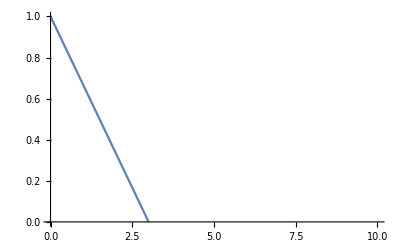

```mathematica
Nstar =1 - (numpred*P)/r;
Plot[Nstar/.{P->0.1,r->0.3},{numpred,0,10},PlotRange->{0,1}]
```

```mathematica
drawext = Table[
mu = 1 - (numpred*P)/r/.{P->1,r->3};
rv=RandomVariate[NormalDistribution[mu,1],1000];
,{numpred,0,10,0.1}
];
```

```mathematica
PrExt= Probability[-Infinity<x<0,x\[Distributed] NormalDistribution[μ,σ]]
```

1/2 Erfc[μ/(√2 σ)]

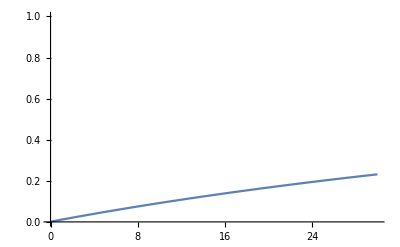

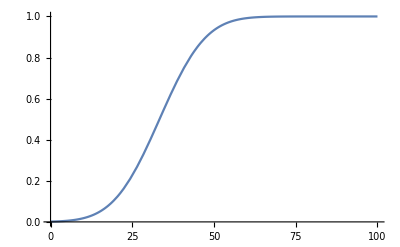

```mathematica
Plot[(ϵ*n+pb)/(1+ϵ*n)/.{pb->0.001,ϵ->0.01},{n,0,30},PlotRange->{0,1}]
Plot[PrExt/.{μ->1-n*ϵ/.{ϵ->0.03},σ->1/3},{n,0,100},PlotRange->{0,1}]
```

```mathematica
PrExt/.{μ->1-0*ϵ/.{ϵ->0.05},σ->0.33}
```

0.00122154